```mathematica
VelocityField[x_, z_, d_,k_, σ_]:=(2 k (x z Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]+x z Cosh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]-2 d k σ^2 Sin[(2 d k x z)/(z^2+4 k^2 σ^4)]-d z Sinh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]))/((z^2+4 k^2 σ^4) (Cos[(2 d k x z)/(z^2+4 k^2 σ^4)]+Cosh[(4 d k^2 x σ^2)/(z^2+4 k^2 σ^4)]))
```

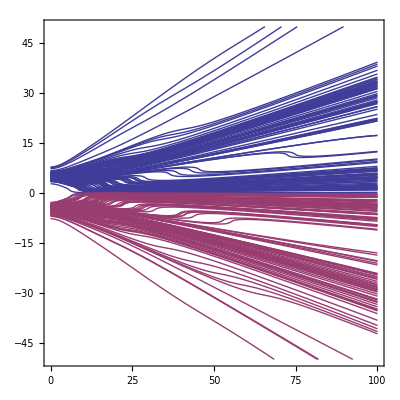

```mathematica
ddd = 5.0;
σσσ = 1.0;
kkk = 2.0;
HollandtablU=Table[NDSolve[{D[y[t], t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== 5+ RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,100}],{100}];
HollandtablD=Table[NDSolve[{D[y[t],t]==1/(2 kkk)VelocityField[y[t], t, ddd,kkk, σσσ ],y[0]== -5+RandomVariate[NormalDistribution[0, σσσ]]},y,{t,0,100}],{100}];
Plot[{y[t]/.HollandtablU,y[t]/.HollandtablD},{t,0,100}, PlotRange->{{0,100},{-50,50}},Frame->True,Axes->True,AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

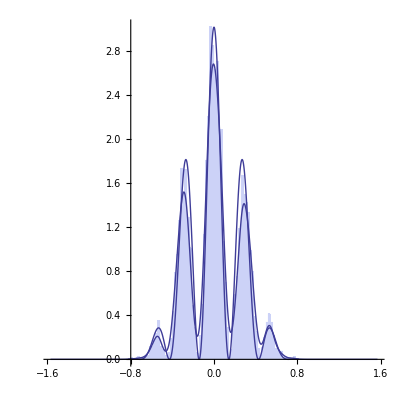

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/BohmianDataDouble2k.dat"]];
Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],SmoothHistogram[ReadDataSingle,0.03,PlotStyle->Thick],Plot[2.0(ⅇ^(-Sec[x]^2/0.4^2))/(π Erfc[1/0.4])Cos[11x]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

```mathematica
Table[Plot[{yyyHank[0,y,t,1,1],yyyHankRand[0,y,t,1,1],yyyCosRand[0,y,t,1,1]},{y,-20,20}],{t,0,10}];
```

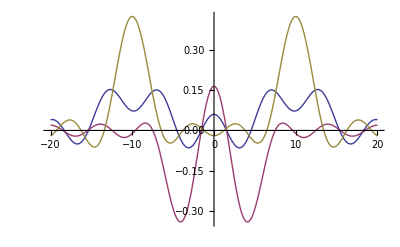

```mathematica
Plot[{yyyHank[0,y,0,1,1],-yyyHankRand[0,y,0,1,1],yyyCosRand[0,y,0,1,1]},{y,-20,20},PlotRange->All]
```

```mathematica
yyyCosRand[x_,y_,t_,k_,w_]=Sum[(Sin[k √(x^2+(y-d)^2)]/√(x^2+(y-d)^2) +Sin[k √(x^2+(y+d)^2)]/√(x^2+(y+d)^2) )/(50),{d,10+RandomVariate[UniformDistribution[{-2,2}],25]}];
```

```mathematica
yyyHankRand[x_,y_,t_,k_,w_]=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t]+BesselJ[0,k √(x^2+(y+d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y+d)^2)] Sin[w t])/(40),{d,5+RandomVariate[UniformDistribution[{-2,2}],20]}];
```

```mathematica
yyyHank[x_,y_,t_,k_,w_]:=Sum[(BesselJ[0,k √(x^2+(y-d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y-d)^2)] Sin[w t]+BesselJ[0,k √(x^2+(y+d)^2)] Cos[w t]+BesselY[0,k √(x^2+(y+d)^2)] Sin[w t])/(18),{d,6,14,1}]
```

```mathematica
DaForceX[x_,y_,t_,k_,w_] = -D[-yyyHankRand[x,y,t,k,w],x];
DaForceY[x_,y_,t_,k_,w_] = -D[-yyyHankRand[x,y,t,k,w],y];
DaForceSingleX[x_,y_,t_,k_,w_] = -D[-yyyHankSingle[x,y,t,k,w],x];
DaForceSingleY[x_,y_,t_,k_,w_] = -D[-yyyHankSingle[x,y,t,k,w],y];
CosDisSqWidth[d_] = ProbabilityDistribution[Cos[x π/(2d)]^2/2,{x,-d,d}]
GaussianTanDisSqWidth[d_,σ_] = ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]
```

ProbabilityDistribution[1/2 Cos[(x π)/(2 d)]^2,{x,-d,d}]

ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]

```mathematica
HydroForceY[y_] = -D[yyyHankRand[0,y,0,1,1],y];
HydroForceX[x_] = -D[yyyHankRand[x,5,0,1,1],x];
HydroForceTanhY[y_] = -Tanh[D[yyyHankRand[0,y,0,1,1],y]];
HydroForceTanhX[x_] = -Tanh[D[yyyHankRand[x,5,0,1,1],x]];
```

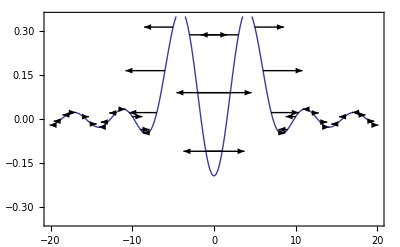

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[0.03],Arrow[{{y,yyyHankRand[0,y,0,1,1]},{y+30HydroForceY[y],yyyHankRand[0,y,0,1,1]}}]}],{y,-20,20}];
Show[Plot[{yyyHankRand[0,y,0,1,1]},{y,-20,20},PlotRange->{Full,{-0.35,0.35}},Frame->True,Axes->True,FrameTicks->{True,True}],MyForceTestArrows]
```

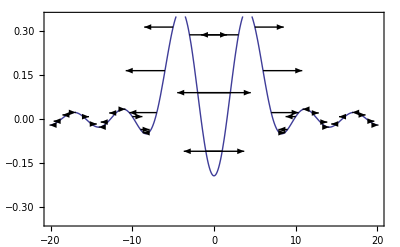

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[0.03],Arrow[{{y,yyyHankRand[0,y,0,1,1]},{y+30HydroForceTanhY[y],yyyHankRand[0,y,0,1,1]}}]}],{y,-20,20}];
Show[Plot[{yyyHankRand[0,y,0,1,1]},{y,-20,20},PlotRange->{Full,{-0.35,0.35}},Frame->True,Axes->True,FrameTicks->{True,True}],MyForceTestArrows]
```

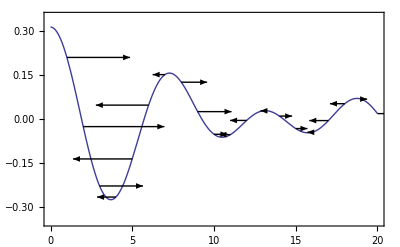

```mathematica
MyForceTestArrows = Table[Graphics[{Arrowheads[0.03],Arrow[{{x,yyyHankRand[x,5,0,1,1]},{x+20HydroForceX[x],yyyHankRand[x,5,0,1,1]}}]}],{x,0,20}];
Show[Plot[{yyyHankRand[x,5,0,1,1]},{x,0,20},PlotRange->{Full,{-0.35,0.35}},Frame->True,Axes->True,FrameTicks->{True,True}],MyForceTestArrows]
```

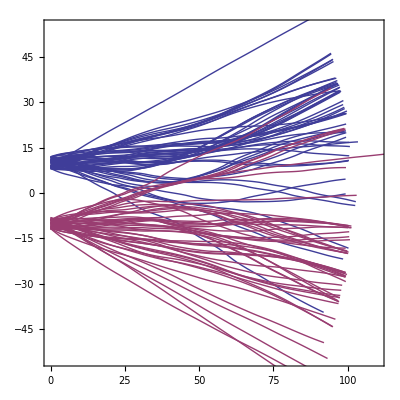

```mathematica
AAA =  1.0;
ddd = 10.0;
www = 2.0;
x000 = 0.0;
v000 = 1.0;
kkk= 2.0;
disss = 0.0;
tmax = 100;
xmax = 110;
NMAX=50;
swidth = 2;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

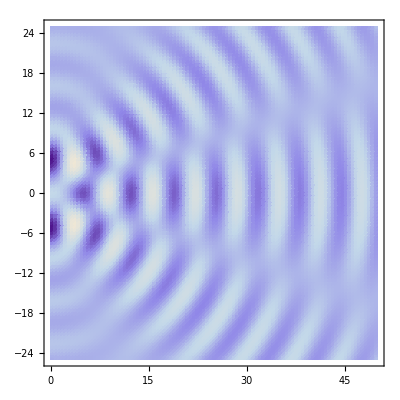

```mathematica
DensityPlot[yyyHankRand[x,y,0,1,10], {x,0,50},{y,-25,25},PlotPoints->{100,100}]
```

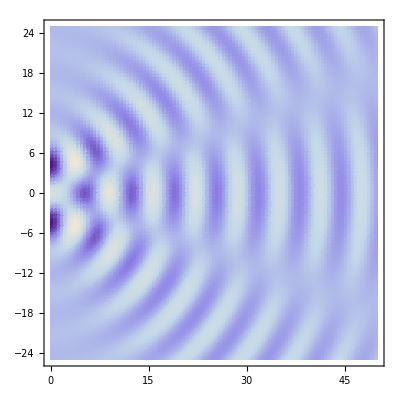

```mathematica
DensityPlot[yyyHankRand[x,y,0,1,1], {x,0,50},{y,-25,25},PlotPoints->{100,100}]
```

```mathematica
anitabletori = Table[DensityPlot[yyyHankRand[x,y,t,1,1], {x,0,20},{y,-10,10},PlotPoints->{50,50}],{t,0,10,1}];
```

```mathematica
ListAnimate[anitabletori]
```

```mathematica
AAA =  1.0;
ddd = 5.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.001;
tmax = 60;
NMAX=50;
swidth = 2;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,tmax},{-tmax/2,tmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

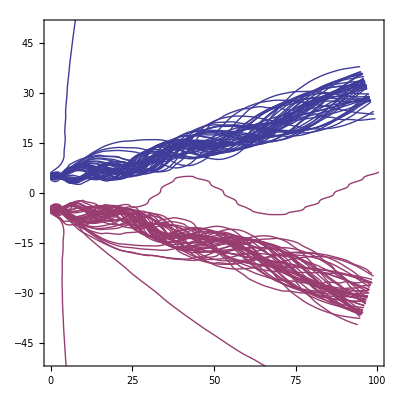

```mathematica
AAA =  10.0;
ddd = 5.0;
www = 2;
x000 = 0.0;
v000 = 1.0;
kkk= 2;
disss = 0.0;
tmax = 100;
NMAX=50;
swidth = 2;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-1,1}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-1,1}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,tmax},{-tmax/2,tmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA = 1.0;
ddd = 4.0;
www = 1;
x000 = 0.0;
v000 = 1.0;
kkk= 1;
disss = 0.0;
tmax = 60;
CHUNK = 10;
REPEAT = 100;
CUTTOFF = 50;

outstream=OpenAppend["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitC50W1D4.dat"];

Do[

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t,kkk,www]-disss (D[x[t],t]), D[y[t],t,t] == AAA DaForceY[x[t],y[t],t,kkk,www]-disss(D[y[t],t]),y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t,kkk,www]-disss (D[x[t],t]), D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t,kkk,www]-disss (D[y[t],t]),y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{CHUNK}];


TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

$Aborted

/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitC50W1D4.dat

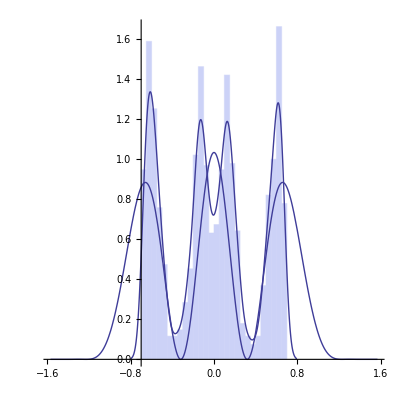

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitC50W1D4.dat"]];

Show[{Histogram[ReadDataSingle,20,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],SmoothHistogram[ReadDataSingle,0.04,PlotStyle->Thick],Plot[2.0(ⅇ^(-Sec[x]^2/2.0^2))/(π Erfc[1/2.0])Cos[5Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

```mathematica
AAA = 1.0;
ddd = 4.0;
www = 1;
x000 = 0.0;
v000 = 1.0;
kkk= 1;
disss = 0.0;
tmax = 60;
CHUNK = 10;
REPEAT = 100;
CUTTOFF = 50;
MEMORY = 50;

outstream=OpenAppend["HydroDoubleSlitM50W1.dat"];

Do[
Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA DaForceX[x[t],y[t],t,kkk,www]-disss (D[x[t],t])), D[y[t],t,t] == ⅇ^(-t/MEMORY)(AAA DaForceY[x[t],y[t],t,kkk,www]-disss(D[y[t],t])),y[0]== 5+RandomVariate[UniformDistribution[{-2,2}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{CHUNK}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  ⅇ^(-t/MEMORY)(AAA DaForceX[x[t],y[t],t,kkk,www]-disss (D[x[t],t])), D[y[t],t,t] ==ⅇ^(-t/MEMORY)( AAA  DaForceY[x[t],y[t],t,kkk,www]-disss (D[y[t],t])),y[0]== -5+RandomVariate[UniformDistribution[{-2,2}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{CHUNK}];

TestTableXU[t_] = Flatten[x[t]/.Hollandtabl3DU];
TestTableYU[t_] = Flatten[y[t]/.Hollandtabl3DU];
TestTableXD[t_] = Flatten[x[t]/.Hollandtabl3DD];
TestTableYD[t_] = Flatten[y[t]/.Hollandtabl3DD];

HistTableAngle = {};
For[NNN = 1,NNN<=Length[TestTableXU[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXU[ttt][[NNN]]^2+TestTableYU[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYU[ttt][[NNN]]/TestTableXU[ttt][[NNN]]]];Break[]]]
]
For[NNN = 1,NNN<=Length[TestTableXD[qqq]],NNN++,
For[ttt=1,ttt < tmax, ttt++, If[(TestTableXD[ttt][[NNN]]^2+TestTableYD[ttt][[NNN]]^2)>CUTTOFF^2,AppendTo[HistTableAngle,ArcTan[TestTableYD[ttt][[NNN]]/TestTableXD[ttt][[NNN]]]];Break[]]]
];

Export[outstream,HistTableAngle]

WriteString[outstream,"\n"]
,{REPEAT}];

Close[outstream]
```

HydroDoubleSlitM100A05.dat

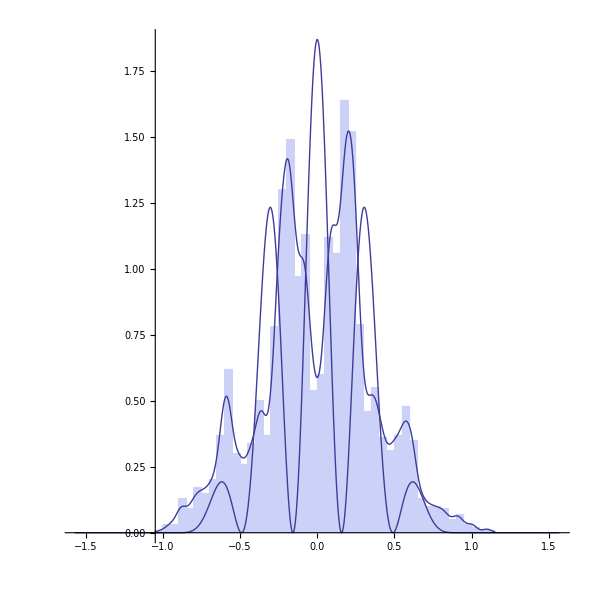

```mathematica
ReadDataSingle = Flatten[Import["HydroDoubleSlitM100A05.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],SmoothHistogram[ReadDataSingle,0.03,PlotStyle->Thick],Plot[1.5(ⅇ^(-Sec[x]^2/0.5^2))/(π Erfc[1/0.5])Cos[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```

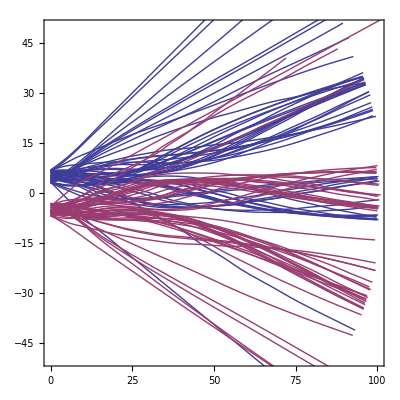

```mathematica
AAA =  1.0;
ddd = 5.0;
www = 2;
x000 = 0.0;
v000 = 1.0;
kkk= 2;
disss = 0.0;
tmax = 100;
NMAX=50;
swidth = 2;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-2,2}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-2,2}]],y'[0]== v000 Sin[RandomVariate[CosDisSqWidth[1]]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,tmax},{-tmax/2,tmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

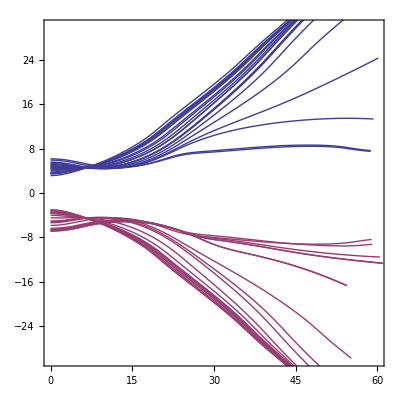

```mathematica
AAA =  1.0;
ddd = 5.0;
www = 1.0;
x000 = 0.0;
v000 = 0.5;
kkk= 1.0;
disss = 0.0;
tmax = 60;
xmax = 60;
NMAX=20;
swidth = 2;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== 0 ,x[0]== x000,x'[0]==v000},{x,y},{t,0,tmax}],{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== 0 ,x[0]== x000,x'[0]==v000},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

```mathematica
AAA =  1.0;
ddd = 5.0;
www = 1.0;
x000 = 0.0;
v000 = 1.0;
kkk= 1.0;
disss = 0.0;
tmax = 60;
xmax = 60;
NMAX=20;
swidth = 2;

Hollandtabl3DU=Table[NDSolve[{D[x[t],t,t] ==  AAA DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA DaForceY[x[t],y[t],t,kkk,www]-disss  D[y[t],t],y[0]== ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]== RandomVariate[NormalDistribution[0,0.5]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
Hollandtabl3DD=Table[NDSolve[{D[x[t],t,t] ==  AAA  DaForceX[x[t],y[t],t,kkk,www]-disss  D[x[t],t], D[y[t],t,t] == AAA  DaForceY[x[t],y[t],t,kkk,www]-disss D[y[t],t],y[0]== -ddd+RandomVariate[UniformDistribution[{-swidth,swidth}]],y'[0]==  RandomVariate[NormalDistribution[0,0.5]] ,x[0]== x000,x'[0]==√(1-y'[0]^2)},{x,y},{t,0,tmax}],{NMAX}];
ParametricPlot[{{x[t],y[t]}/.Hollandtabl3DU,{x[t],y[t]}/.Hollandtabl3DD},{t,0,tmax},PlotRange->{{0,xmax},{-xmax/2,xmax/2}},Frame->True,Axes->True, AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}]
```

NDSolve::ndsz: At t == 0.0676651, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.0970296, step size is effectively zero; singularity or stiff system suspected.

$Aborted

$Aborted

```mathematica
GaussianTanDisSqWidth[d_,σ_] = ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]
```

ProbabilityDistribution[(ⅇ^(-Sec[x]^2/σ^2))/(π Erfc[1/σ]),{x,-d,d}]

```mathematica
Manipulate[Plot[ⅇ^(-Sin[ϕ]^2/σ^2) ,{ϕ,-π,π},PlotRange->{Full,{0,1}}],{σ,1,10}]
```

```mathematica
Manipulate[Plot[ⅇ^(-ϕ^2/σ^2) Cos[ϕ]^2,{ϕ,-π,π},PlotRange->{Full,{0,1}}],{σ,10,0.1}]
```

```mathematica
Integrate[ⅇ^(-x^2/σ^2 - ⅈ x p),{x,-d,d}]
```

1/2 ⅇ^(-1/4 p^2 σ^2) √π σ (Erf[d/σ-(ⅈ p σ)/2]+Erf[d/σ+(ⅈ p σ)/2])

```mathematica
FullSimplify[(Erf[d/σ-(ⅈ p σ)/2]+Erf[d/σ+(ⅈ p σ)/2])(Erf[d/σ+(ⅈ p σ)/2]+Erf[d/σ-(ⅈ p σ)/2])]
```

(Erf[d/σ-(ⅈ p σ)/2]+Erf[d/σ+(ⅈ p σ)/2])^2

```mathematica
Manipulate[Plot[ⅇ^(-1/2 p^2 σ^2)(Erf[d/σ-(ⅈ p σ)/2]+Erf[d/σ+(ⅈ p σ)/2])^2,{p,-π,π},PlotRange->{Full,{0,1}}],{σ,10,0.1},{d,1,5}]
```

```mathematica
Manipulate[Plot[Sinc[d π Sin[p]]^2,{p,-π/2,π/2},PlotRange->{Full,{0,1}}],{σ,10,0.1},{d,0.1,5}]
```

```mathematica
Integrate[Cos[x π/(2d)]^2/2,{x,-π/2,π/2}]
```

(π^2+2 d Sin[π^2/(2 d)])/(4 π)

```mathematica
Cos[x]^2/(π/2)
```

(2 Cos[x]^2)/π

```mathematica
Integrate[Cos[x]^2/(π/2),{x,-π/2,π/2}]
```

1

```mathematica
Manipulate[Plot[{(Sinc[x π/(d)]^2)/(d ),Sinc[x π/(d)]^2/2,Cos[x]^2/2},{x,-π/2,π/2},PlotRange->{Full,{0,1}}],{σ,10,0.1},{d,0.1,1}]
```

```mathematica
Integrate[(Sinc[x π/(d)]^2)/(d ),{x,-∞,∞},Assumptions:>1/d∈Reals]
```

√(1/d^2) d

```mathematica
FullSimplify[Integrate[(Sinc[Sin[x] π/(2d)]^2)/(2 d),{x,-π/2,π/2},Assumptions:>1/d∈Reals]]
```

(BesselJ[1,π/d] (-2 d+π^2 StruveH[0,π/d])+π BesselJ[0,π/d] (2-π StruveH[1,π/d]))/(2 d)

```mathematica
Manipulate[Plot[Cos[x π/(2d)]^2/2,{x,-π/2,π/2},PlotRange->{Full,{0,1}}],{σ,10,0.1},{d,0.1,5}]
```

```mathematica
Manipulate[Plot[{((ϕ+ddd)/swidth),Sin[((ϕ+ddd)/swidth)π/2]} ,{ϕ,-π,π},PlotRange->{Full,{-1,1}}],{ddd,0,5},{swidth,1,5}]
```

```mathematica
Manipulate[Plot[ⅇ^(-ϕ^2/(2 σ^2)) ,{ϕ,-π,π},PlotRange->{Full,{0,1}}],{σ,1,5}]
```

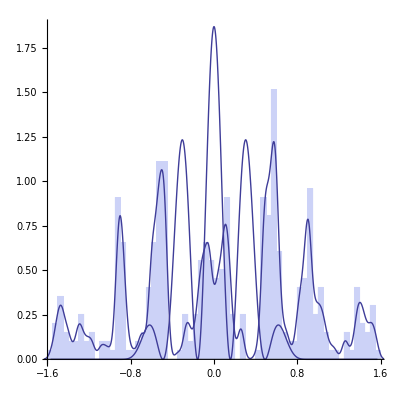

```mathematica
ReadDataSingle = Flatten[Import["/Users/cricha5/Desktop/Physics/ASimpleModelOfQuandrops/Mathematica/HydroDoubleSlitAngles.dat"]];

Show[{Histogram[ReadDataSingle,50,"PDF",PlotRange->{{-π/2,π/2},Full},Axes->{True,False},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->14}],SmoothHistogram[ReadDataSingle,0.03,PlotStyle->Thick],Plot[1.5(ⅇ^(-Sec[x]^2/0.5^2))/(π Erfc[1/0.5])Cos[10Sin[x]]^2,{x,-π/2,π/2},PlotRange->{Full,{0,4}}]}]
```